```mathematica
<<X`
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

The trace of  [Γ^+(p.γ+m_p)γ^+(p’.γ+m_p)]

```mathematica
Tr1=Spur[γ.(k+q),γ5,𝟙(2 Subscript[k, μ]+Subscript[q, μ]),γ.(p-k)+m 𝟙,γ.(-k),γ5,γ.p+mp 𝟙,Subscript[γ, ν],γ.p1+mp 𝟙]/.{p.p->mp^2,p1.p1->mp^2,p.p1->-q.q/2+mp^2,𝒹->4,p.q->(-q.q)/2,p1.q->(q.q)/2,Subscript[k, μ]->k1,Subscript[k, ν]->k1,Subscript[p, ν]->P1-q1/2,Subscript[p, μ]->P1-q1/2,Subscript[p1, ν]->P1+q1/2,Subscript[p1, μ]->P1+q1/2,Subscript[q, μ]->q1,Subscript[q, ν]->q1}
```

-8 k^2 k1^2 (mp^2-q^2/2)+8 k^2 k1^2 mp^2+8 k^2 k1 m mp (P1-q1/2)+8 k^2 k1 m mp (P1+q1/2)+8 k^2 k1 mp^2 (P1-q1/2)+8 k^2 k1 mp^2 (P1+q1/2)-12 k^2 k1 q1 (mp^2-q^2/2)+12 k^2 k1 mp^2 q1+8 k^2 k1 k.p (P1+q1/2)+8 k^2 k1 k.p1 (P1-q1/2)+4 k^2 k1 q^2 (P1-q1/2)-4 k^2 k1 q^2 (P1+q1/2)+4 k^2 m mp q1 (P1-q1/2)+4 k^2 m mp q1 (P1+q1/2)+4 k^2 mp^2 q1 (P1-q1/2)+4 k^2 mp^2 q1 (P1+q1/2)-4 k^2 q1^2 (mp^2-q^2/2)+4 k^2 mp^2 q1^2+4 k^2 q1 k.p (P1+q1/2)+4 k^2 q1 k.p1 (P1-q1/2)+2 k^2 q^2 q1 (P1-q1/2)-2 k^2 q^2 q1 (P1+q1/2)+16 k1^2 k.p (mp^2-q^2/2)-16 k1^2 mp^2 k.p+8 k1 m mp q1 k.p-8 k1 m mp q1 k.p1+8 k1 m mp k.q (P1-q1/2)+8 k1 m mp k.q (P1+q1/2)+24 k1 q1 k.p (mp^2-q^2/2)-16 k1 mp^2 q1 k.p-8 k1 mp^2 q1 k.p1+8 k1 mp^2 k.q (P1-q1/2)+8 k1 mp^2 k.q (P1+q1/2)-16 k1 k.p k.p1 (P1-q1/2)-8 k1 q^2 k.p (P1-q1/2)+8 k1 q^2 k.p (P1+q1/2)-16 k1 (k.p)^2 (P1+q1/2)+4 m mp q1^2 k.p-4 m mp q1^2 k.p1+4 m mp q1 k.q (P1-q1/2)+4 m mp q1 k.q (P1+q1/2)+8 q1^2 k.p (mp^2-q^2/2)-4 mp^2 q1^2 k.p-4 mp^2 q1^2 k.p1+4 mp^2 q1 k.q (P1-q1/2)+4 mp^2 q1 k.q (P1+q1/2)-8 q1 k.p k.p1 (P1-q1/2)-4 q^2 q1 k.p (P1-q1/2)+4 q^2 q1 k.p (P1+q1/2)-8 q1 (k.p)^2 (P1+q1/2)+8 k1^2 m mp q^2+8 k1^2 mp^2 q^2+4 k1 m mp q^2 q1+4 k1 mp^2 q^2 q1

Replace k^2 to be D_π(k^2)+M_π^2, k.p to be (D_(n(p-k))-D_(π(k))+m^2-mp^2-M^2)/(-2).

```mathematica
ETr1=Tr1//.{k.k->Subscript[D, π(k)]+M^2,k.q->(Subscript[D, π(k+q)]-Subscript[D, π(k)]-q.q)/2,
k.p1->k.p+k.q,k.p->(Subscript[D, n(p-k)]-Subscript[D, π(k)]+m^2-mp^2-M^2)/-2}
```

8 mp^2 q^2 k1^2+8 m mp q^2 k1^2+8 mp^2 (M^2+D^(k π)) k1^2-8 (mp^2-q^2/2) (M^2+D^(k π)) k1^2-8 mp^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1^2+8 (mp^2-q^2/2) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1^2-4 (P1+q1/2) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))^2 k1+4 mp^2 q1 q^2 k1+4 m mp q1 q^2 k1+8 mp^2 (P1-q1/2) (M^2+D^(k π)) k1+8 m mp (P1-q1/2) (M^2+D^(k π)) k1+8 mp^2 (P1+q1/2) (M^2+D^(k π)) k1+8 m mp (P1+q1/2) (M^2+D^(k π)) k1+12 mp^2 q1 (M^2+D^(k π)) k1-12 q1 (mp^2-q^2/2) (M^2+D^(k π)) k1+4 (P1-q1/2) q^2 (M^2+D^(k π)) k1-4 (P1+q1/2) q^2 (M^2+D^(k π)) k1-8 mp^2 q1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1+4 m mp q1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1+12 q1 (mp^2-q^2/2) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1-4 (P1-q1/2) q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1+4 (P1+q1/2) q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1+4 (P1+q1/2) (M^2+D^(k π)) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) k1+4 mp^2 (P1-q1/2) (-q^2-D^(k π)+D^(π (k+q))) k1+4 m mp (P1-q1/2) (-q^2-D^(k π)+D^(π (k+q))) k1+4 mp^2 (P1+q1/2) (-q^2-D^(k π)+D^(π (k+q))) k1+4 m mp (P1+q1/2) (-q^2-D^(k π)+D^(π (k+q))) k1-8 mp^2 q1 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) k1-8 m mp q1 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) k1+8 (P1-q1/2) (M^2+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) k1-8 (P1-q1/2) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) k1-2 (P1+q1/2) q1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))^2+4 mp^2 q1^2 (M^2+D^(k π))+4 mp^2 (P1-q1/2) q1 (M^2+D^(k π))+4 m mp (P1-q1/2) q1 (M^2+D^(k π))+4 mp^2 (P1+q1/2) q1 (M^2+D^(k π))+4 m mp (P1+q1/2) q1 (M^2+D^(k π))-4 q1^2 (mp^2-q^2/2) (M^2+D^(k π))+2 (P1-q1/2) q1 q^2 (M^2+D^(k π))-2 (P1+q1/2) q1 q^2 (M^2+D^(k π))-2 mp^2 q1^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+2 m mp q1^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+4 q1^2 (mp^2-q^2/2) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))-2 (P1-q1/2) q1 q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+2 (P1+q1/2) q1 q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+2 (P1+q1/2) q1 (M^2+D^(k π)) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+2 mp^2 (P1-q1/2) q1 (-q^2-D^(k π)+D^(π (k+q)))+2 m mp (P1-q1/2) q1 (-q^2-D^(k π)+D^(π (k+q)))+2 mp^2 (P1+q1/2) q1 (-q^2-D^(k π)+D^(π (k+q)))+2 m mp (P1+q1/2) q1 (-q^2-D^(k π)+D^(π (k+q)))-4 mp^2 q1^2 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q))))-4 m mp q1^2 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q))))+4 (P1-q1/2) q1 (M^2+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q))))-4 (P1-q1/2) q1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q))))

Divided by the propagator and regulator

```mathematica
DTr1=Simplify[Expand[ETr1]/(Subscript[D, Λ(k)]^2 Subscript[D, π(k)] Subscript[D, n(p-k)] Subscript[D, Λ(k+q)]^2 Subscript[D, π(k+q)])]
```

1/(D^(π k) (D^(k Λ))^2 D^(π (k+q)) D^(n (p-k)) (D^(Λ (k+q)))^2)(2 k1+q1) (q^2 (2 k1-2 P1+q1) (D^(n (p-k))+(m+mp)^2)+D^(n (p-k)) ((2 P1-q1) D^(π (k+q))+D^(π k) (2 P1+q1)+4 P1 (-2 m^2+M^2+2 mp^2))-((m+mp)^2 ((q1-2 P1) D^(π (k+q))-D^(π k) (2 P1+q1)+4 P1 (m^2-2 m mp-M^2+mp^2)))-4 P1 (D^(n (p-k)))^2)

The propagators in the light cone frame.

```mathematica
bbb:={Subscript[D, Λ(k+q)]:>(k1+q1)(k2+q2-(DotProduct[(k+q),(k+q)]+Λ^2)/(k1+q1)),
Subscript[D, π(k+q)]:>(k1+q1)(k2+q2-(DotProduct[(k+q),(k+q)]+M^2)/(k1+q1)),
Subscript[D, Λ(k)]:>k1(k2-(DotProduct[k,k]+Λ^2)/k1),
Subscript[D, π(k)]:>k1(k2-(DotProduct[k,k]+M^2)/k1),
Subscript[D, n(p-k)]:>(k1-(1+ξ)P1)(k2-P2-(DotProduct[k+q/2,k+q/2]+m^2)/(k1-(1+ξ)P1))}
```

Calculating the integral of k^- using the residual theorem

The first region is 0<k^+<-q^+,  the corresponding region of y is  [-ξ, ξ].

```mathematica
FTr1=-2π*I*Residue[DTr1/.bbb,{k2,(DotProduct[k,k]+Λ^2)/k1}]-2π*I*Residue[DTr1/.bbb,{k2,(DotProduct[k,k]+M^2)/k1}]
```

-(2 ⅈ k1 π (2 k1+q1) (-4 P1 P2^2 k1^4-2 P1 P2 q2 k1^4+P2 q1 q2 k1^4-2 P2 q^2 k1^4+310+2 M^2 P1 q1^2 ξ DotProduct(k,k)-4 M^2 P1^2 q1 ξ DotProduct(k,k)))/((M^2-Λ^2)^2 (-P2 k1^2-m^2 k1+M^2 k1+13) (q2 k1^2+q1 q2 k1+1-1+M^2 q1+q1 DotProduct(k,k)) (q2 k1^2+M^2 k1-Λ^2 k1+1+1-DotProduct(1) k1+M^2 q1+q1 DotProduct(k,k))^2)-(2 4 (1))/1
 |  |  |  |

```mathematica
FSTr1a=FTr1[[1]]//.{k1->(y+ξ)*P1,q1->-2ξ*P1,P2->(1-ξ)*(mp^2+Q^2/4)/P1,q2->(q.q+DotProduct[q,q])/q1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q.q->-Q^2,k.k->k^2,DotProduct[k,q]->DotProduct[q,k],DotProduct[k+q,k+q]->(k^2+2DotProduct[k,q]+DotProduct[q,q]),DotProduct[k+q/2,k+q/2]->(k^2+DotProduct[k,q]+DotProduct[q,q]/4)};
```

```mathematica
FSTr1b=FTr1[[2]]//.{k1->(y+ξ)*P1,q1->-2ξ*P1,P2->(1-ξ)*(mp^2-(q.q)/4)/P1,q2->(q.q+DotProduct[q,q])/q1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q.q->-Q^2,k.k->k^2,DotProduct[k,q]->DotProduct[q,k],DotProduct[k+q,k+q]->(k^2+2DotProduct[k,q]+DotProduct[q,q]),DotProduct[k+q/2,k+q/2]->(k^2+DotProduct[k,q]+DotProduct[q,q]/4)};
```

The first region is -q^+<k^+<(1+ξ)P^+,  the corresponding region of y is  [ξ, 1].

```mathematica
FTr1c=2π*I*Residue[DTr1/.bbb,{k2,P2+(DotProduct[k+q/2,k+q/2]+m^2)/(k1-(1+ξ)P1)}]
```

-((2 ⅈ π (2 k1+q1) (k1-P1-P1 ξ)^4 (-4 P1^2 m^4+q1^2 m^4-2 P1 q1 m^4-4 P1^2 ξ m^4+2 mp q1^2 m^3-8 k1 mp P1 m^3-4 mp P1 q1 m^3+8 mp^2 P1^2 m^2+mp^2 q1^2 m^2+k1 P2 q1^2 m^2-P1 P2 q1^2 m^2-12 k1 mp^2 P1 m^2+4 k1 P1^2 P2 m^2-4 k1^2 P1 P2 m^2-2 mp^2 P1 q1 m^2+2 P1^2 P2 q1 m^2-2 k1 P1 P2 q1 m^2+2 k1 P1^2 q2 m^2+k1 q1^2 q2 m^2-P1 q1^2 q2 m^2-2 k1^2 P1 q2 m^2+k1^2 q1 q2 m^2+2 P1^2 q1 q2 m^2-3 k1 P1 q1 q2 m^2+8 mp^2 P1^2 ξ m^2-P1 P2 q1^2 ξ m^2+4 k1 P1^2 P2 ξ m^2+2 P1^2 P2 q1 ξ m^2+2 k1 P1^2 q2 ξ m^2-P1 q1^2 q2 ξ m^2+2 P1^2 q1 q2 ξ m^2-k1 P1 q1 q2 ξ m^2-2 P1^2 DotProduct(k,k) m^2+2 k1 P1 DotProduct(k,k) m^2+k1 q1 DotProduct(k,k) m^2-P1 q1 DotProduct(k,k) m^2-2 P1^2 ξ DotProduct(k,k) m^2-P1 q1 ξ DotProduct(k,k) m^2+q1^2 DotProduct(k+q/2,k+q/2) m^2-4 k1 P1 DotProduct(k+q/2,k+q/2) m^2-2 P1 q1 DotProduct(k+q/2,k+q/2) m^2-2 P1^2 DotProduct(k+q,k+q) m^2+2 k1 P1 DotProduct(k+q,k+q) m^2-k1 q1 DotProduct(k+q,k+q) m^2+P1 q1 DotProduct(k+q,k+q) m^2-2 P1^2 ξ DotProduct(k+q,k+q) m^2+P1 q1 ξ DotProduct(k+q,k+q) m^2-2 k1^2 q^2 m^2-2 P1^2 q^2 m^2+4 k1 P1 q^2 m^2-k1 q1 q^2 m^2+P1 q1 q^2 m^2-2 P1^2 ξ q^2 m^2+2 k1 P1 ξ q^2 m^2+P1 q1 ξ q^2 m^2+2 k1 mp P2 q1^2 m-2 mp P1 P2 q1^2 m+8 k1 mp P1^2 P2 m-8 k1^2 mp P1 P2 m+4 mp P1^2 P2 q1 m-4 k1 mp P1 P2 q1 m+4 k1 mp P1^2 q2 m+2 k1 mp q1^2 q2 m-2 mp P1 q1^2 q2 m-4 k1^2 mp P1 q2 m+4 mp P1^2 q1 q2 m+2 k1^2 mp q1 q2 m-6 k1 mp P1 q1 q2 m-2 mp P1 P2 q1^2 ξ m+8 k1 mp P1^2 P2 ξ m+4 mp P1^2 P2 q1 ξ m+4 k1 mp P1^2 q2 ξ m-2 mp P1 q1^2 q2 ξ m+4 mp P1^2 q1 q2 ξ m-2 k1 mp P1 q1 q2 ξ m-4 mp P1^2 DotProduct(k,k) m+4 k1 mp P1 DotProduct(k,k) m+2 k1 mp q1 DotProduct(k,k) m-2 mp P1 q1 DotProduct(k,k) m-4 mp P1^2 ξ DotProduct(k,k) m-2 mp P1 q1 ξ DotProduct(k,k) m+2 mp q1^2 DotProduct(k+q/2,k+q/2) m-8 k1 mp P1 DotProduct(k+q/2,k+q/2) m-4 mp P1 q1 DotProduct(k+q/2,k+q/2) m-4 mp P1^2 DotProduct(k+q,k+q) m+4 k1 mp P1 DotProduct(k+q,k+q) m-2 k1 mp q1 DotProduct(k+q,k+q) m+2 mp P1 q1 DotProduct(k+q,k+q) m-4 mp P1^2 ξ DotProduct(k+q,k+q) m+2 mp P1 q1 ξ DotProduct(k+q,k+q) m-4 mp P1^2 q^2 m-4 k1^2 mp q^2 m+8 k1 mp P1 q^2 m-2 k1 mp q1 q^2 m+2 mp P1 q1 q^2 m-4 mp P1^2 ξ q^2 m+4 k1 mp P1 ξ q^2 m+2 mp P1 q1 ξ q^2 m-4 mp^4 P1^2+k1 mp^2 P2 q1^2-mp^2 P1 P2 q1^2+4 k1 mp^4 P1+4 k1 mp^2 P1^2 P2-4 k1^2 mp^2 P1 P2+2 mp^2 P1^2 P2 q1-2 k1 mp^2 P1 P2 q1+2 k1 mp^2 P1^2 q2+k1 mp^2 q1^2 q2-mp^2 P1 q1^2 q2-2 k1^2 mp^2 P1 q2+k1^2 mp^2 q1 q2+2 mp^2 P1^2 q1 q2-3 k1 mp^2 P1 q1 q2-4 mp^4 P1^2 ξ-mp^2 P1 P2 q1^2 ξ+4 k1 mp^2 P1^2 P2 ξ+2 mp^2 P1^2 P2 q1 ξ+2 k1 mp^2 P1^2 q2 ξ-mp^2 P1 q1^2 q2 ξ+2 mp^2 P1^2 q1 q2 ξ-k1 mp^2 P1 q1 q2 ξ-2 mp^2 P1^2 DotProduct(k,k)+2 k1 mp^2 P1 DotProduct(k,k)+k1 mp^2 q1 DotProduct(k,k)-mp^2 P1 q1 DotProduct(k,k)-2 mp^2 P1^2 ξ DotProduct(k,k)-mp^2 P1 q1 ξ DotProduct(k,k)+mp^2 q1^2 DotProduct(k+q/2,k+q/2)-4 k1 mp^2 P1 DotProduct(k+q/2,k+q/2)-2 mp^2 P1 q1 DotProduct(k+q/2,k+q/2)-2 mp^2 P1^2 DotProduct(k+q,k+q)+2 k1 mp^2 P1 DotProduct(k+q,k+q)-k1 mp^2 q1 DotProduct(k+q,k+q)+mp^2 P1 q1 DotProduct(k+q,k+q)-2 mp^2 P1^2 ξ DotProduct(k+q,k+q)+mp^2 P1 q1 ξ DotProduct(k+q,k+q)-2 k1^2 mp^2 q^2-2 mp^2 P1^2 q^2+4 k1 mp^2 P1 q^2-k1 mp^2 q1 q^2+mp^2 P1 q1 q^2-2 mp^2 P1^2 ξ q^2+2 k1 mp^2 P1 ξ q^2+mp^2 P1 q1 ξ q^2))/((P2 k1^2+m^2 k1-M^2 k1-P1 P2 k1-P1 P2 ξ k1-DotProduct(k,k) k1+DotProduct(k+q/2,k+q/2) k1+M^2 P1+M^2 P1 ξ+P1 DotProduct(k,k)+P1 ξ DotProduct(k,k)) (P2 k1^2+m^2 k1-Λ^2 k1-P1 P2 k1-P1 P2 ξ k1-DotProduct(k,k) k1+DotProduct(k+q/2,k+q/2) k1+P1 Λ^2+P1 Λ^2 ξ+P1 DotProduct(k,k)+P1 ξ DotProduct(k,k))^2 (P2 k1^2+q2 k1^2+m^2 k1-M^2 k1-P1 P2 k1+P2 q1 k1-P1 q2 k1+q1 q2 k1-P1 P2 ξ k1-P1 q2 ξ k1+DotProduct(k+q/2,k+q/2) k1-DotProduct(k+q,k+q) k1+M^2 P1+m^2 q1-P1 P2 q1-P1 q1 q2+M^2 P1 ξ-P1 P2 q1 ξ-P1 q1 q2 ξ+q1 DotProduct(k+q/2,k+q/2)+P1 DotProduct(k+q,k+q)+P1 ξ DotProduct(k+q,k+q)) (P2 k1^2+q2 k1^2+m^2 k1-Λ^2 k1-P1 P2 k1+P2 q1 k1-P1 q2 k1+q1 q2 k1-P1 P2 ξ k1-P1 q2 ξ k1+DotProduct(k+q/2,k+q/2) k1-DotProduct(k+q,k+q) k1+P1 Λ^2+m^2 q1-P1 P2 q1-P1 q1 q2+P1 Λ^2 ξ-P1 P2 q1 ξ-P1 q1 q2 ξ+q1 DotProduct(k+q/2,k+q/2)+P1 DotProduct(k+q,k+q)+P1 ξ DotProduct(k+q,k+q))^2))

```mathematica
FSTr1c=FTr1c//.{k1->(y+ξ)*P1,q1->-2ξ*P1,P2->(1-ξ)*(mp^2-(q.q)/4)/P1,q2->(q.q+DotProduct[q,q])/q1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q.q->-Q^2,k.k->k^2,DotProduct[k,q]->DotProduct[q,k],DotProduct[k+q,k+q]->(k^2+2DotProduct[k,q]+DotProduct[q,q]),DotProduct[k+q/2,k+q/2]->(k^2+DotProduct[k,q]+DotProduct[q,q]/4)};
```

The trace of  [Γ^+(p.γ+m_p)(p’.γ+m_p)]P^+/m_p

```mathematica
Tr2=Spur[γ.(k+q),γ5,𝟙(2 Subscript[k, μ]+Subscript[q, μ]),γ.(p-k)+m 𝟙,γ.(-k),γ5,γ.p+mp 𝟙,γ.p1+mp 𝟙]*P1/mp/.{p.p->mp^2,p1.p1->mp^2,p.p1->-q.q/2+mp^2,𝒹->4,p.q->(-q.q)/2,p1.q->(q.q)/2,Subscript[k, μ]->k1,Subscript[k, ν]->k1,Subscript[p, ν]->P1-q1/2,Subscript[p, μ]->P1-q1/2,Subscript[p1, ν]->P1+q1/2,Subscript[p, 1μ]->P1+q1/2,Subscript[q, μ]->q1,Subscript[q, ν]->q1}
```

1/mp P1 (8 k^2 k1 m (mp^2-q^2/2)+8 k^2 k1 m mp^2+8 k^2 k1 mp (mp^2-q^2/2)+8 k^2 k1 mp^3+8 k^2 k1 mp k.p+8 k^2 k1 mp k.p1+4 k^2 m q1 (mp^2-q^2/2)+4 k^2 m mp^2 q1+4 k^2 mp q1 (mp^2-q^2/2)+4 k^2 mp^3 q1+4 k^2 mp q1 k.p+4 k^2 mp q1 k.p1+8 k1 m k.q (mp^2-q^2/2)+8 k1 m mp^2 k.q+4 k1 m q^2 k.p+4 k1 m q^2 k.p1+8 k1 mp k.q (mp^2-q^2/2)+8 k1 mp^3 k.q-16 k1 mp k.p k.p1+4 k1 mp q^2 k.p-16 k1 mp (k.p)^2+4 k1 mp q^2 k.p1+4 m q1 k.q (mp^2-q^2/2)+4 m mp^2 q1 k.q+2 m q^2 q1 k.p+2 m q^2 q1 k.p1+4 mp q1 k.q (mp^2-q^2/2)+4 mp^3 q1 k.q-8 mp q1 k.p k.p1+2 mp q^2 q1 k.p-8 mp q1 (k.p)^2+2 mp q^2 q1 k.p1)

```mathematica
ETr2=Tr2//.{k.k->Subscript[D, π(k)]+M^2,k.q->(Subscript[D, π(k+q)]-Subscript[D, π(k)]-q.q)/2,
k.p1->k.p+k.q,k.p->(Subscript[D, n(p-k)]-Subscript[D, π(k)]+m^2-mp^2-M^2)/-2}
```

1/mp P1 (8 k1 (M^2+D^(k π)) mp^3+4 q1 (M^2+D^(k π)) mp^3+4 k1 (-q^2-D^(k π)+D^(π (k+q))) mp^3+2 q1 (-q^2-D^(k π)+D^(π (k+q))) mp^3+8 k1 m (M^2+D^(k π)) mp^2+4 m q1 (M^2+D^(k π)) mp^2+4 k1 m (-q^2-D^(k π)+D^(π (k+q))) mp^2+2 m q1 (-q^2-D^(k π)+D^(π (k+q))) mp^2-4 k1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))^2 mp-2 q1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))^2 mp+8 k1 (mp^2-q^2/2) (M^2+D^(k π)) mp+4 q1 (mp^2-q^2/2) (M^2+D^(k π)) mp+2 k1 q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) mp+q1 q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) mp+4 k1 (M^2+D^(k π)) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) mp+2 q1 (M^2+D^(k π)) (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) mp+4 k1 (mp^2-q^2/2) (-q^2-D^(k π)+D^(π (k+q))) mp+2 q1 (mp^2-q^2/2) (-q^2-D^(k π)+D^(π (k+q))) mp+4 k1 q^2 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) mp+2 q1 q^2 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) mp+8 k1 (M^2+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) mp+4 q1 (M^2+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) mp-8 k1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) mp-4 q1 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π)) (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))) mp+8 k1 m (mp^2-q^2/2) (M^2+D^(k π))+4 m q1 (mp^2-q^2/2) (M^2+D^(k π))+2 k1 m q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+m q1 q^2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+4 k1 m (mp^2-q^2/2) (-q^2-D^(k π)+D^(π (k+q)))+2 m q1 (mp^2-q^2/2) (-q^2-D^(k π)+D^(π (k+q)))+4 k1 m q^2 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q))))+2 m q1 q^2 (1/2 (-m^2+M^2+mp^2-D^(n (p-k))+D^(k π))+1/2 (-q^2-D^(k π)+D^(π (k+q)))))

```mathematica
DTr2=Simplify[Expand[ETr2]/(Subscript[D, Λ(k)]^2 Subscript[D, π(k)] Subscript[D, n(p-k)] Subscript[D, Λ(k+q)]^2 Subscript[D, π(k+q)])]
```

-1/(mp D^(π k) (D^(k Λ))^2 D^(π (k+q)) D^(n (p-k)) (D^(Λ (k+q)))^2)2 P1 (2 k1+q1) (mp (D^(n (p-k)) (-D^(π (k+q))-D^(π k)+4 m^2-2 M^2-4 mp^2)+(m+mp)^2 (-D^(π (k+q))-D^(π k)+2 (m^2-2 m mp-M^2+mp^2))+2 (D^(n (p-k)))^2)+q^2 ((m+2 mp) D^(n (p-k))+m (m+mp)^2))

Calculating the integral of k^- using the residual theorem

The first region is 0<k^+<-q^+,  the corresponding region of y is  [-ξ, ξ].

```mathematica
FTr2=-2π*I*Residue[DTr2/.bbb,{k2,(DotProduct[k,k]+Λ^2)/k1}]-2π*I*Residue[DTr2/.bbb,{k2,(DotProduct[k,k]+M^2)/k1}]
```

(4 ⅈ k1 P1 π (2 k1+q1) (2 k1^2 mp^5-6 k1^2 M^2 mp^3+4 k1 M^2 P1 mp^3+192+k1^2 m DotProduct(k,k) q^2-k1 m P1 DotProduct(k,k) q^2-k1 m P1 ξ DotProduct(k,k) q^2-k1^2 m DotProduct(k+q/2,k+q/2) q^2))/(mp (M^2-Λ^2)^2 (-P2 k1^2-m^2 k1+14) (q2 k1^2+q1 q2 k1+DotProduct(k,k) k1-DotProduct(k+q,k+q) k1+M^2 q1+q1 DotProduct(k,k)) (q2 k1^2+M^2 k1-Λ^2 k1+4+M^2 q1+q1 DotProduct(k,k))^2)-(4 5 (1))/(mp 3 1^2)
 |  |  |  |

```mathematica
FSTr2a=FTr2[[1]]//.{k1->(y+ξ)*P1,q1->-2ξ*P1,P2->(1-ξ)*(mp^2-(q.q)/4)/P1,q2->(q.q+DotProduct[q,q])/q1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q.q->-Q^2,k.k->k^2,DotProduct[k,q]->DotProduct[q,k],DotProduct[k+q,k+q]->(k^2+2DotProduct[k,q]+DotProduct[q,q]),DotProduct[k+q/2,k+q/2]->(k^2+DotProduct[k,q]+DotProduct[q,q]/4)};
```

```mathematica
FSTr2b=FTr2[[2]]//.{k1->(y+ξ)*P1,q1->-2ξ*P1,P2->(1-ξ)*(mp^2-(q.q)/4)/P1,q2->(q.q+DotProduct[q,q])/q1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q.q->-Q^2,k.k->k^2,DotProduct[k,q]->DotProduct[q,k],DotProduct[k+q,k+q]->(k^2+2DotProduct[k,q]+DotProduct[q,q]),DotProduct[k+q/2,k+q/2]->(k^2+DotProduct[k,q]+DotProduct[q,q]/4)};
```

The first region is -q^+<k^+<(1+ξ)P^+,  the corresponding region of y is  [ξ, 1].

```mathematica
FTr2c=2π*I*Residue[DTr2/.bbb,{k2,P2+(DotProduct[k+q/2,k+q/2]+m^2)/(k1-(1+ξ)P1)}]
```

(4 ⅈ P1 π (2 k1+q1) (-k1+P1+P1 ξ)^4 (-2 k1 mp^5+2 P1 mp^5+2 P1 ξ mp^5+6 k1 m^2 mp^3-4 m^2 P1 mp^3+2 k1^2 P2 mp^3-2 k1 P1 P2 mp^3+m^2 q1 mp^3+k1 P2 q1 mp^3-P1 P2 q1 mp^3+k1^2 q2 mp^3-k1 P1 q2 mp^3+k1 q1 q2 mp^3-P1 q1 q2 mp^3-4 m^2 P1 ξ mp^3-2 k1 P1 P2 ξ mp^3-P1 P2 q1 ξ mp^3-k1 P1 q2 ξ mp^3-P1 q1 q2 ξ mp^3-k1 DotProduct(k,k) mp^3+P1 DotProduct(k,k) mp^3+P1 ξ DotProduct(k,k) mp^3+2 k1 DotProduct(k+q/2,k+q/2) mp^3+q1 DotProduct(k+q/2,k+q/2) mp^3-k1 DotProduct(k+q,k+q) mp^3+P1 DotProduct(k+q,k+q) mp^3+P1 ξ DotProduct(k+q,k+q) mp^3+4 k1 m^3 mp^2+4 k1^2 m P2 mp^2-4 k1 m P1 P2 mp^2+2 m^3 q1 mp^2+2 k1 m P2 q1 mp^2-2 m P1 P2 q1 mp^2+2 k1^2 m q2 mp^2-2 k1 m P1 q2 mp^2+2 k1 m q1 q2 mp^2-2 m P1 q1 q2 mp^2-4 k1 m P1 P2 ξ mp^2-2 m P1 P2 q1 ξ mp^2-2 k1 m P1 q2 ξ mp^2-2 m P1 q1 q2 ξ mp^2-2 k1 m DotProduct(k,k) mp^2+2 m P1 DotProduct(k,k) mp^2+2 m P1 ξ DotProduct(k,k) mp^2+4 k1 m DotProduct(k+q/2,k+q/2) mp^2+2 m q1 DotProduct(k+q/2,k+q/2) mp^2-2 k1 m DotProduct(k+q,k+q) mp^2+2 m P1 DotProduct(k+q,k+q) mp^2+2 m P1 ξ DotProduct(k+q,k+q) mp^2-k1 m q^2 mp^2+m P1 q^2 mp^2+m P1 ξ q^2 mp^2+2 m^4 P1 mp+2 k1^2 m^2 P2 mp-2 k1 m^2 P1 P2 mp+m^4 q1 mp+k1 m^2 P2 q1 mp-m^2 P1 P2 q1 mp+k1^2 m^2 q2 mp-k1 m^2 P1 q2 mp+k1 m^2 q1 q2 mp-m^2 P1 q1 q2 mp+2 m^4 P1 ξ mp-2 k1 m^2 P1 P2 ξ mp-m^2 P1 P2 q1 ξ mp-k1 m^2 P1 q2 ξ mp-m^2 P1 q1 q2 ξ mp-k1 m^2 DotProduct(k,k) mp+m^2 P1 DotProduct(k,k) mp+m^2 P1 ξ DotProduct(k,k) mp+2 k1 m^2 DotProduct(k+q/2,k+q/2) mp+m^2 q1 DotProduct(k+q/2,k+q/2) mp-k1 m^2 DotProduct(k+q,k+q) mp+m^2 P1 DotProduct(k+q,k+q) mp+m^2 P1 ξ DotProduct(k+q,k+q) mp-2 k1 m^2 q^2 mp+2 m^2 P1 q^2 mp+2 m^2 P1 ξ q^2 mp-k1 m^3 q^2+m^3 P1 q^2+m^3 P1 ξ q^2))/(mp (-P2 k1^2-m^2 k1+Λ^2 k1+P1 P2 k1+P1 P2 ξ k1+DotProduct(k,k) k1-DotProduct(k+q/2,k+q/2) k1-P1 Λ^2-P1 Λ^2 ξ-P1 DotProduct(k,k)-P1 ξ DotProduct(k,k))^2 (P2 k1^2+m^2 k1-M^2 k1-P1 P2 k1-P1 P2 ξ k1-DotProduct(k,k) k1+DotProduct(k+q/2,k+q/2) k1+M^2 P1+M^2 P1 ξ+P1 DotProduct(k,k)+P1 ξ DotProduct(k,k)) (-P2 k1^2-q2 k1^2-m^2 k1+Λ^2 k1+P1 P2 k1-P2 q1 k1+P1 q2 k1-q1 q2 k1+P1 P2 ξ k1+P1 q2 ξ k1-DotProduct(k+q/2,k+q/2) k1+DotProduct(k+q,k+q) k1-P1 Λ^2-m^2 q1+P1 P2 q1+P1 q1 q2-P1 Λ^2 ξ+P1 P2 q1 ξ+P1 q1 q2 ξ-q1 DotProduct(k+q/2,k+q/2)-P1 DotProduct(k+q,k+q)-P1 ξ DotProduct(k+q,k+q))^2 (P2 k1^2+q2 k1^2+m^2 k1-M^2 k1-P1 P2 k1+P2 q1 k1-P1 q2 k1+q1 q2 k1-P1 P2 ξ k1-P1 q2 ξ k1+DotProduct(k+q/2,k+q/2) k1-DotProduct(k+q,k+q) k1+M^2 P1+m^2 q1-P1 P2 q1-P1 q1 q2+M^2 P1 ξ-P1 P2 q1 ξ-P1 q1 q2 ξ+q1 DotProduct(k+q/2,k+q/2)+P1 DotProduct(k+q,k+q)+P1 ξ DotProduct(k+q,k+q)))

```mathematica
FSTr2c=FTr2c//.{k1->(y+ξ)*P1,q1->-2ξ*P1,P2->(1-ξ)*(mp^2-(q.q)/4)/P1,q2->(q.q+DotProduct[q,q])/q1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q.q->-Q^2,k.k->k^2,DotProduct[k,q]->DotProduct[q,k],DotProduct[k+q,k+q]->(k^2+2DotProduct[k,q]+DotProduct[q,q]),DotProduct[k+q/2,k+q/2]->(k^2+DotProduct[k,q]+DotProduct[q,q]/4)};
```

Spliting function f

```mathematica
f1=k*(4 mp^2 ξ^2*(FSTr2a+FSTr2b)-Q^2*(FSTr1a+FSTr1b))/(8*P1(4 mp^2 ξ^2+(ξ^2-1)Q^2))//. {DotProduct[q,k]->k*q*Cos[θ],DotProduct[k,q]->k*q*Cos[θ],DotProduct[k,k]->k^2,P1->1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q1->-2ξ*P1}
```

(k (4 mp^2 ξ^2 ((4 ⅈ π (y+ξ) (2 (y+ξ)-2 ξ) (1))/(mp (M^2-Λ^2)^2 (1) (-2 ξ k^2+8) (1)^2)-(4 4 (1))/(mp 3 1^2))-Q^2 (1)))/(8 ((ξ^2-1) Q^2+4 mp^2 ξ^2))
 |  |  |  |

```mathematica
f2=k*(4 mp^2 ξ^2*(FSTr2c)-Q^2*(FSTr1c))/(8*P1(4 mp^2 ξ^2+(ξ^2-1)Q^2))//. {DotProduct[q,k]->k*q*Cos[θ],DotProduct[k,q]->k*q*Cos[θ],DotProduct[k,k]->k^2,P1->1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q};
```

Spliting function g

```mathematica
g1=k*(mp^2(1-ξ^2)*(FSTr2a+FSTr2b)-mp^2*(FSTr1a+FSTr1b))/(2*P1(4 mp^2 ξ^2+(ξ^2-1)Q^2))//. {DotProduct[q,k]->k*q*Cos[θ],DotProduct[k,q]->k*q*Cos[θ],DotProduct[k,k]->k^2,P1->1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q,q1->-2ξ*P1};
```

```mathematica
g2=k*(mp^2(1-ξ^2)*(FSTr2c)-mp^2*(FSTr1c))/(2*P1(4 mp^2 ξ^2+(ξ^2-1)Q^2))//. {DotProduct[q,k]->k*q*Cos[θ],DotProduct[k,q]->k*q*Cos[θ],DotProduct[k,k]->k^2,P1->1,DotProduct[q,q]->-(2ξ)^2 mp^2-(1-ξ^2)q.q};
```

check if the integral is xi independent

```mathematica
m=110;
mp=94;
f=9.4;
ξ=0.3;
Λ=110;
M=14;
q.q=-10000;
Q=Sqrt[-q.q];
q=Sqrt[-4 ξ^2 mp^2-(1-ξ^2)q.q];
```

```mathematica
1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f1,{k,0,∞},{θ,0,2π},{y,-ξ,ξ},WorkingPrecision->15]+NIntegrate[f2,{k,0,∞},{θ,0,2π},{y,ξ,1}])
```

0.+0.00448965 ⅈ

```mathematica
1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[g1,{k,0,∞},{θ,0,2π},{y,-ξ,ξ},WorkingPrecision->15]+NIntegrate[g2,{k,0,∞},{θ,0,2π},{y,ξ,1}])
```

0.+0.0725582 ⅈ

```mathematica
m=110;
mp=94;
f=9.4;
ξ=0.1;
Λ=110;
M=14;
q.q=-10000;
Q=Sqrt[-q.q];
q=Sqrt[-4 ξ^2 mp^2-(1-ξ^2)q.q];
```

```mathematica
1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f1,{k,0,∞},{θ,0,2π},{y,-ξ,ξ},WorkingPrecision->15]+NIntegrate[f2,{k,0,∞},{θ,0,2π},{y,ξ,1}])
```

0.+0.00448965 ⅈ

```mathematica
1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[g1,{k,0,∞},{θ,0,2π},{y,-ξ,ξ},WorkingPrecision->15]+NIntegrate[g2,{k,0,∞},{θ,0,2π},{y,ξ,1}])
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.+0.0725582 ⅈ

```mathematica
Clear[m,mp,f,ξ,Λ,M,Q,q]
q.q=.
```

Plot splitting functions

```mathematica
m=94;
mp=94;
f=9.4;
ξ=0.3;
Λ=110;
M=14;
q.q=-10000;
Q=Sqrt[-q.q];
q=Sqrt[-4 ξ^2 mp^2-(1-ξ^2)q.q];
```

```mathematica
aa=Table[-I 1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)NIntegrate[f2,{k,0,∞},{θ,0,2π},WorkingPrecision->15],{y,ξ,1,0.01}];
```

$Aborted

```mathematica
bb=Table[-I 1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)NIntegrate[f1,{k,0,∞},{θ,0,2π},WorkingPrecision->15],{y,-ξ,ξ,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
cc=Table[-I 1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)NIntegrate[g2,{k,0,∞},{θ,0,2π},WorkingPrecision->15],{y,ξ,1,0.01}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
dd=Table[-I 1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)NIntegrate[g1,{k,0,∞},{θ,0,2π},WorkingPrecision->15],{y,-ξ,ξ,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

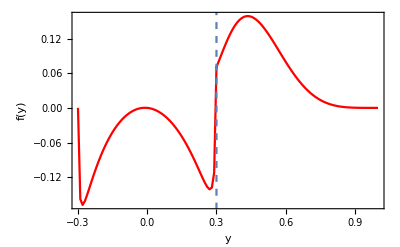

```mathematica
Show[ListLinePlot[Join[Transpose[{Range[-ξ,ξ,0.01],Re[bb]}],Transpose[{Range[ξ,1,0.01],Re[aa]}]],Frame->True,FrameLabel->{Style["y",15,Black],Style["f(y)",15,Black]},PlotStyle->Red],ListLinePlot[{{0.3,-0.2},{0.3,0.2}},PlotStyle->Dashed]]
```

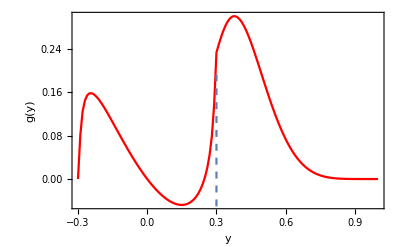

```mathematica
Show[ListLinePlot[Join[Transpose[{Range[-ξ,ξ,0.01],Re[dd]}],Transpose[{Range[ξ,1,0.01],Re[cc]}]],Frame->True,FrameLabel->{Style["y",15,Black],Style["g(y)",15,Black]},PlotStyle->Red],ListLinePlot[{{0.3,-0.2},{0.3,0.2}},PlotStyle->Dashed]]
```

Sea quark GPD in DGLAP region

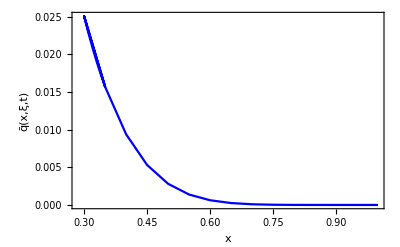

```mathematica
ListLinePlot[Join[Transpose[{Range[ξ,ξ+0.05,0.01],Re[-I%647]}],Transpose[{Range[ξ,1,0.05],Re[-I%531]}]],Frame->True,Frame->True,FrameLabel->{Style["x",15,Black],Style["q̄(x,ξ,t)",15,Black]},PlotStyle->Blue]
```

```mathematica
HDG[x_,ξ_,t_]:=1/(1+t/6870)1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y(h[β,(x-β)/ξ]*vπ[β])/ξ,{β,(x-ξ)/(1-ξ),(x+ξ)/(1+ξ)},{k,0,∞},{θ,0,2π},{y,x,1},MinRecursion->10,MaxRecursion->20,WorkingPrecision->10,AccuracyGoal->10])
```

```mathematica
ff[x_]:=NIntegrate[x+y,{y,x,1}]
```

```mathematica
ff[3]
```

-10.

```mathematica
(0.4-ξ)/(1-ξ)
```

0.142857

```mathematica
NIntegrate[(h[β,(0.4-β)/ξ]*vπ[β])/ξ,{β,(0.4-ξ)/(1-ξ),(0.4+ξ)/(1+ξ)},WorkingPrecision->10]*NIntegrate[10^12 f2/y,{k,0,∞},{θ,0,2π},{y,0.4,1}]
```

0.+1.20579 ⅈ

```mathematica
(h[β,(0.4-β)/ξ]*vπ[β])/ξ/.β->(0.4-ξ)/(1-ξ)+0.001
```

0.000196979

```mathematica
Table[NIntegrate[10^12 f2/y(h[β,(0.4-β)/ξ]*vπ[β])/ξ,{k,0,∞},{θ,0,2π},{y,0.4,1}],{β,0.2,0.3,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.}

```mathematica
NIntegrate[10^12 f2/y(h[β,(0.4-β)/ξ]*vπ[β])/ξ,{k,0,∞},{θ,0,2π},{y,0.4,1},{β,(0.4-ξ)/(1-ξ)+0.000001,(0.4+ξ)/(1+ξ)},MinRecursion->10,MaxRecursion->20,WorkingPrecision->10,AccuracyGoal->10]
```

0

```mathematica
NIntegrate[10^12 1/y(h[β,(0.4-β)/ξ]*vπ[β])/ξ*f2/k^4,{k,0,∞},{θ,0,2π},{y,0.4,1},{β,(0.4-ξ)/(1-ξ),(0.4+ξ)/(1+ξ)},MinRecursion->10,MaxRecursion->20,WorkingPrecision->10,AccuracyGoal->10]
```

0

```mathematica
x=0.4
```

0.4

```mathematica
NIntegrate[f2/y(h[β,(x/y-β)/(0.3/y)] vπ[β])/(0.3/y),{y,0.4,1},{β,(x/y-0.3/y)/(1-0.3/y),(x/y+0.3/y)/(1+0.3/y)},{k,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->20,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

$Aborted

```mathematica
DG1=Join[Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y q2[x/y,ξ/y,10000],{k,0,∞},{θ,0,2π},{y,x,1},WorkingPrecision->10]),{x,ξ,ξ+0.04,0.01}],Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y q2[x/y,ξ/y,10000],{k,0,∞},{θ,0,2π},{y,x,1},WorkingPrecision->10]),{x,ξ+0.05,1,0.05}]]
```

NIntegrate::nlim: β = 0.6/((1.+0.3/y) y) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.+0.0250911 ⅈ,0.+0.0228941 ⅈ,0.+0.0208774 ⅈ,0.+0.0190163 ⅈ,0.+0.0172946 ⅈ,0.+0.0157011 ⅈ,0.+0.00939545 ⅈ,0.+0.0053104 ⅈ,0.+0.00281287 ⅈ,0.+0.00138289 ⅈ,0.+0.000622582 ⅈ,0.+0.000251799 ⅈ,0.+0.0000889119 ⅈ,0.+0.0000262213 ⅈ,0.+5.99433×10^-6 ⅈ,0.+9.23231×10^-7 ⅈ,0.+6.98614×10^-8 ⅈ,0.+9.4628×10^-10 ⅈ,0.}

```mathematica
EB1=Join[Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y q1[x/y,ξ/y,10000],{k,0,∞},{θ,0,2π},{y,ξ,1},WorkingPrecision->10]),{x,-ξ,ξ-0.05,0.05}],Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y q1[x/y,ξ/y,10000],{k,0,∞},{θ,0,2π},{y,ξ,1},WorkingPrecision->10]),{x,ξ-0.04,ξ,0.01}]]
```

NIntegrate::nlim: β = -0.6/((1.+0.3/y) y) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.-0.000902201 ⅈ,0.-0.00442945 ⅈ,0.-0.00593058 ⅈ,0.-0.00225809 ⅈ,0.+0.00682248 ⅈ,0.+0.019908 ⅈ,0.+0.0346174 ⅈ,0.+0.0480875 ⅈ,0.+0.0573991 ⅈ,0.+0.0600603 ⅈ,0.+0.0546361 ⅈ,0.+0.0417314 ⅈ,0.+0.0385488 ⅈ,0.+0.0352903 ⅈ,0.+0.0320373 ⅈ,0.+0.0288923 ⅈ,0.+0.0259934 ⅈ}

```mathematica
Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y q1[x/y,ξ/y,10000],{k,0,∞},{θ,0,2π},{y,ξ,1},WorkingPrecision->10]),{x,ξ-0.05,ξ,0.01}]
```

NIntegrate::nlim: β = 0.55/((1.+0.3/y) y) is not a valid limit of integration.

NIntegrate::nlim: β = -0.05/((1.+0.3/y) y) is not a valid limit of integration.

NIntegrate::nlim: β = 0.55/((1.+0.3/y) y) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{0.+0.0417314 ⅈ,0.+0.0385488 ⅈ,0.+0.0352903 ⅈ,0.+0.0320373 ⅈ,0.+0.0288923 ⅈ,0.+0.0259934 ⅈ}

```mathematica
ListLinePlot[Join[Transpose[{Range[-ξ,ξ,0.05],Re[-I%45]}],Transpose[{Range[ξ-0.05,ξ,0.01],Re[-I%46]}]],Frame->True,Frame->True,FrameLabel->{Style["x",15,Black],Style["q̄(x,ξ,t)",15,Black]},PlotStyle->Blue]
```

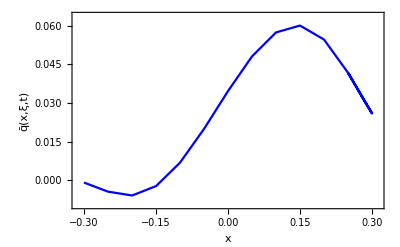

```mathematica
EB2=Join[Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f1/(2y)DA[(x/ξ+1)/2,(y/ξ+1)/2,10000],{k,0,∞},{θ,0,2π},{y,-ξ,ξ},WorkingPrecision->10]),{x,-ξ,ξ-0.05,0.05}],Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f1/(2y)DA[(x/ξ+1)/2,(y/ξ+1)/2,10000],{k,0,∞},{θ,0,2π},{y,-ξ,ξ},WorkingPrecision->10]),{x,ξ-0.04,ξ,0.01}]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,0.-0.0109195 ⅈ,0.-0.0198536 ⅈ,0.-0.0268024 ⅈ,0.-0.0317658 ⅈ,0.-0.0347439 ⅈ,0.-0.0357366 ⅈ,0.-0.0347439 ⅈ,0.-0.0317658 ⅈ,0.-0.0268024 ⅈ,0.-0.0198536 ⅈ,0.-0.0109195 ⅈ,0.-0.00889443 ⅈ,0.-0.00678995 ⅈ,0.-0.00460604 ⅈ,0.-0.00234273 ⅈ,0.}

```mathematica
Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f1/(2y)DA[(x/ξ+1)/2,(y/ξ+1)/2,10000],{k,0,∞},{θ,0,2π},{y,-ξ,ξ},WorkingPrecision->10]),{x,ξ-0.05,ξ,0.01}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.-0.0109195 ⅈ,0.-0.00889443 ⅈ,0.-0.00678995 ⅈ,0.-0.00460604 ⅈ,0.-0.00234273 ⅈ,0.}

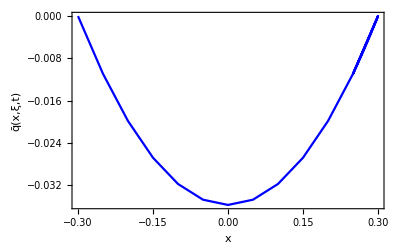

```mathematica
ListLinePlot[Join[Transpose[{Range[-ξ,ξ,0.05],Re[-I%49]}],Transpose[{Range[ξ-0.05,ξ,0.01],Re[-I%48]}]],Frame->True,Frame->True,FrameLabel->{Style["x",15,Black],Style["q̄(x,ξ,t)",15,Black]},PlotStyle->Blue]
```

```mathematica
ListLinePlot[Join[Transpose[{Range[-ξ,ξ,0.05],Re[-I%49]}],Transpose[{Range[ξ-0.05,ξ,0.01],Re[-I%48]}]],Frame->True,Frame->True,FrameLabel->{Style["x",15,Black],Style["q̄(x,ξ,t)",15,Black]},PlotStyle->Blue]
```

```mathematica
Re[-I(EB1+EB2)]
```

{-0.000902201,-0.015349,-0.0257842,-0.0290605,-0.0249433,-0.0148358,-0.00111917,0.0133436,0.0256332,0.0332579,0.0347825,0.0308119,0.0296544,0.0285004,0.0274312,0.0265496,0.0259934}

```mathematica
DG1=Join[Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y q2[x/y,ξ/y,10000],{k,0,∞},{θ,0,2π},{y,x,1},WorkingPrecision->10]),{x,ξ,ξ+0.04,0.01}],Table[1.26^2/(2 f^2)((Λ^2-M^2)^4)/(2(2π)^4)(NIntegrate[f2/y q2[x/y,ξ/y,10000],{k,0,∞},{θ,0,2π},{y,x,1},WorkingPrecision->10]),{x,ξ+0.05,1,0.05}]]
```

```mathematica
Transpose[{Join[Range[-ξ,ξ-0.05,0.05],Range[ξ-0.04,ξ,0.01]],Re[-I(EB1+EB2)]}]
```

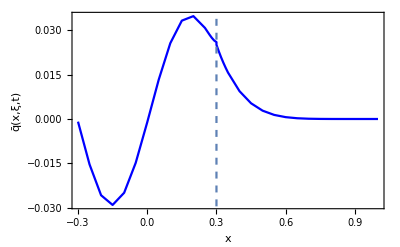

```mathematica
Show[ListLinePlot[Join[Transpose[{Join[Range[-ξ,ξ-0.05,0.05],Range[ξ-0.04,ξ,0.01]],Re[-I(EB1+EB2)]}],Transpose[{Join[Range[ξ,ξ+0.04,0.01],Range[ξ+0.05,1,0.05]],Re[-I*DG1]}]],Frame->True,FrameLabel->{Style["x",15,Black],Style["q̄(x,ξ,t)",15,Black]},PlotStyle->Blue],ListLinePlot[{{0.3,-0.2},{0.3,0.2}},PlotStyle->Dashed]]
```